```mathematica
RowDelete[x_,entries_]:=Module[{list,i},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]
(*ColumnDelete takes a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]
(*AddZeroToRow adds a zero to a row vector*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]
(*AddZerosToRow will add any number of zeros to a row vector*)
AddZerosToRow[x_,entries_]:=Module[{y,list,i},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]


MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c,j,k},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]


ProcessData[raw_,cov_]:=Module[{rawdata,p,tankrow,tanks,purepopdata,logpopdata,covdata,processeddata,index,compdataset,i,i0,j,data},
rawdata=Delete[raw,1];
p=Length[rawdata[[1]]]-cov-1;

tankrow=Delete[raw[[All,1]],1];(*extracts the column of tank labels as a row vector.*)
tanks=DeleteDuplicates[tankrow];(*Just getting a list of tank labels*)

purepopdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤cov,i++,
purepopdata=ColumnDelete[purepopdata,{1}]
];
logpopdata=Log[purepopdata];

If[cov==0,covdata={},
covdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤p,i++,
covdata=ColumnDelete[covdata,{Length[covdata[[1]]]}]
]
];

processeddata=If[cov==0,Transpose[Join[{tankrow},Transpose[logpopdata]]],Transpose[Join[{tankrow},Transpose[covdata],Transpose[logpopdata]]]];(*Join log transformed values back up with tank labels*)

(*Below we extract tank specific processed data and label it by the tank label.*)
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
data[index]={};
For[i=1,i≤Length[processeddata],i++,
i0=If[processeddata[[i,1]]==index,{processeddata[[i]]},{}];
data[index]=Join[data[index],i0]
];
data[index]=ColumnDelete[data[index],{1}]
];

compdataset={};
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
compdataset=Join[compdataset,{data[index]}]
];
compdataset
]
```

```mathematica
SetDirectory["/Users/4/Documents/Weak interactions/tank data"];
rawdata[1]=Import["CER0.csv"];
rawdata[2]=Import["CER_DAP0.csv"];
rawdata[3]=Import["CER_SCA0.csv"];
rawdata[4]=Import["DAP0.csv"];
rawdata[5]=Import["DAPSCA0.csv"];
rawdata[6]=Import["SCA0.csv"];
rawdata[7]=Import["N0.csv"];
rawdata[8]=Import["N_CER0.csv"];
rawdata[9]=Import["N_CER_DAP0.csv"];
rawdata[10]=Import["N_CER_SCA0.csv"];
rawdata[11]=Import["N_DAP0.csv"];
rawdata[12]=Import["N_SCA0.csv"];
rawdata[13]=Import["N_SCA_DAP0.csv"];
rawdata[14]=Import["N_I_DAP0.csv"];
rawdata[15]=Import["N_I0.csv"];
rawdata[16]=Import["N_I_COP0.csv"];
rawdata[17]=Import["CER_SCA_DAP0.csv"];

(*1 covariate*)
rawdata[18]=Import["CER.csv"];
rawdata[19]=Import["CER_DAP.csv"];
rawdata[20]=Import["CER_SCA.csv"];
rawdata[21]=Import["DAP.csv"];
rawdata[22]=Import["DAPSCA.csv"];
rawdata[23]=Import["SCA.csv"];
rawdata[24]=Import["N.csv"];
rawdata[25]=Import["N_CER.csv"];
rawdata[26]=Import["N_CER_DAP.csv"];
rawdata[27]=Import["N_CER_SCA.csv"];
rawdata[28]=Import["N_Dap.csv"];
rawdata[29]=Import["N_Sca.csv"];
rawdata[30]=Import["N_SCA_DAP.csv"];
rawdata[31]=Import["N_I_DAP.csv"];

(*2 covariates*)
rawdata[32]=Import["N_I.csv"];
rawdata[33]=Import["N_I_cop.csv"];

For[i=1,i≤17,i++,
prodata[i]=ProcessData[rawdata[i],0];
m[i]=MAR[prodata[i],0,{}]
]
For[i=18,i≤33,i++,
prodata[i] = ProcessData[rawdata[i],1];
m[i]=MAR[prodata[i],1,{}]
]
```

```mathematica
(*Find distribution of B matrices (for off-diagonal and on-diagonal) and produce some new B matrices to use as "known" B matrices*)
(*Find covariance matrix of Sigma for the data and use that to produce noise*)
(*Refer to picture on your phone*)
(*Actual data took 26 samples from 6 tanks*)
(*Standard deviation for estimated B matrix should be smaller than known B matrix and tests for stability should be the similar if good estimate*)
```

```mathematica
B[D_]:=Module[{p,cov,B},(*extract B matrix*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]]
]
```

```mathematica
For[i=1,i≤17,i++,
p=Length[m[i]];
cov=Length[m[i][[1]]]-p-1;
Amatrix[i] = m[i][[All,1;;1]];
Bmatrix[i] = B[m[i]];
If[cov == 0,
Cmatrix[i] = 0,
Cmatrix[i] = m[i][[All,2;;2+cov-1]]]
]
prodata[1][[1]]
```

{{-3.7966,4.2223,2.33311},{-3.7966,4.67227,-5.29832},{-3.7966,5.59827,3.31273},{-3.7966,4.61542,1.14422},{-0.890054,4.5743,2.7447},{-0.786299,4.65053,1.43031},{-3.7966,4.4666,2.14593},{-0.786299,4.4666,2.14593},{-3.7966,3.00618,0.524729},{-3.7966,3.26995,1.10856},{-3.7966,3.11928,2.1883},{0.523206,3.35446,1.19089},{1.08662,2.99423,2.42392},{1.29314,3.00964,0.722706},{1.40771,3.4128,-5.29832},{2.14771,3.59759,0.392042},{1.64808,4.0189,1.71019},{2.8311,3.95623,2.26696},{0.716171,3.99434,1.81156},{-3.7966,3.91681,1.51513},{-3.7966,3.77826,0.139762},{-0.196907,3.89304,3.13157},{-1.71716,3.55506,0.8671},{-3.10345,3.23514,0.0953102},{-3.7966,5.28973,3.8582},{-2.00484,3.25771,-1.89712}}

```mathematica
For[i=1,i≤17,i++,
noise[i] = {};
For[j=1,j≤Length[prodata[i]],j++,
noiseprep1[j]={};
noiseprep2[j]={};
For[k=1,k≤Length[prodata[i][[j]]]-1,k++,
noiseprep1[j] = Join[noiseprep1[j],{prodata[i][[j,k+1]]-Amatrix[i]-Bmatrix[i].prodata[i][[j,k]]}];
noiseprep2[j] = Join[noiseprep2[j],Transpose[noiseprep1[j][[k]]]]
];
noise[i] =Join[noise[i],{noiseprep2[j]}]
];
covar[i]={};
For[j=1,j≤Length[noise[i]],j++,
covar[i]=Join[covar[i],{Covariance[noise[i][[j]]]}]
]
]
covar[1][[1]]
```

{{3.41615,-0.00477982,0.290084},{-0.00477982,0.401376,0.421965},{0.290084,0.421965,5.28084}}

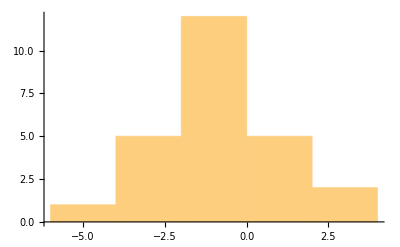

1.84828

```mathematica
Histogram[noise[1][[1,All,1]]]
StandardDeviation[noise[1][[1,All,1]]]
```

```mathematica
(*Using all B matrices*)
odlist = {};
dlist={};
For[i=1,i≤17,i++,
For[j=1,j≤Length[Bmatrix[i]],j++,
For[k=1,k≤Length[Bmatrix[i][[j]]],k++,
If[j≠k,
odlist = Join[odlist,{Bmatrix[i][[j,k]]}],
dlist = Join[dlist,{Bmatrix[i][[j,k]]}]
]
]
]
]
```

```mathematica
(*Using one Bmatrix*)
odlist={};
dlist={};
For[i=1,i≤Length[Bmatrix[1]],i++,
For[j=1,j≤Length[Bmatrix[1][[i]]],j++,
If[i==j,
dlist = Join[dlist,{Bmatrix[1][[i,j]]}],
odlist = Join[odlist,{Bmatrix[1][[i,j]]}]
]
]
]
```

```mathematica
numB = 100;
For[i=1,i≤numB,i++,
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
If[j≠k,
Bmat[j,k]=RandomVariate[NormalDistribution[Bmatrix[1][[j,k]],StandardDeviation[odlist]]],
Bmat[j,k]=RandomVariate[NormalDistribution[Bmatrix[1][[j,k]],StandardDeviation[dlist]]]
]
]
];
TestB[i] = Array[Bmat,{3,3}]
]
(*For[i=1,i≤117,i++,
If[i≤17,
allB[i] = Bmatrix[i],
allB[i] = TestB[i-17]
]
]*)
```

```mathematica
(* Takes hours to run before computer runs out of memory and wipes out data
For[i=1,i≤117,i++,
Sigma[1] = Array[elem,{Length[allB[1][[1]]],Length[allB[1][[1]]]}];
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
elem[j,k]=RandomReal[{-1,1}];
elem[k,j]=elem[j,k];
]
];
Sigma[1] = Sigma[1].Transpose[Sigma[1]];
Et[i] = RandomReal[{-1,1},{maxt,Length[allB[i][[1]]]}].CholeskyDecomposition[Sigma[i]];
Xlist[i] = {};
For[l=1,l≤ Length[prodata[i]],l++,
prep2 = {};
X[0] = prodata[i][[l,1]];
maxt = 1000;
For[m=1,m≤maxt,m++,
X[m] = allB[i].X[m-1]+Transpose[{Et[i][[m]]}];
prep1 = {};
For[n=1,n≤Length[X[m]],n++,
prep1 = Join[prep1,X[m][[n]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[i] = Join[Xlist[i],{prep2}];
];
Bmatrix2[i]=B[MAR[Xlist[i],0,{}]]
]*)
```

```mathematica
(*Only uses B matrices that were produced from the statistical properties of the B matrices from the data*)
maxt = 50;
iter = 50;
For[i=1,i≤numB,i++,
Sigma[i] = Array[elem,{Length[TestB[i][[1]]],Length[TestB[i][[1]]]}];
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
elem[j,k]=RandomReal[{-1,1}];
elem[k,j]=elem[j,k];
]
];
Sigma[i] = Sigma[i].Transpose[Sigma[i]]
]
For[i=1,i≤numB,i++,
Bmatrix2[i] = {};
For[j=1,j≤ iter,j++,
Et[i] = RandomReal[{-.01,.01},{maxt,Length[TestB[i][[1]]]}].CholeskyDecomposition[Sigma[i]];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = prodata[1][[k,1]];
For[l=1,l≤maxt,l++,
X[l] = TestB[i].X[l-1]+Transpose[{Et[i][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[i]=Join[Bmatrix2[i],{prep3}]
]
]
```

```mathematica
For[i=1,i≤numB,i++,
oldodlist[i] = {};
olddlist[i] = {};
newodlist[i] = {};
newdlist[i] = {};
For[k=1,k≤3,k++,
For[l=1,l≤3,l++,
If[k≠l,
oldodlist[i]=Join[oldodlist[i],{TestB[i][[k,l]]}],
olddlist[i]=Join[olddlist[i],{TestB[i][[k,l]]}];
]
]
];
For[j=1,j≤iter,j++,
For[k=1,k≤3,k++,
For[l=1,l≤3,l++,
If[k≠l,
newodlist[i]=Join[newodlist[i],{Bmatrix2[i][[j,k,l]]}],
newdlist[i] = Join[newdlist[i],{Bmatrix2[i][[j,k,l]]}]
]
]
]
];
stdodold[i] = StandardDeviation[oldodlist[i]];
stddold[i]=StandardDeviation[olddlist[i]];
(*stdodknown[i] = StandardDeviation[odlist];
stddknown[i] = StandardDeviation[dlist];*)
stdodest[i] = StandardDeviation[newodlist[i]];
stddest[i] = StandardDeviation[newdlist[i]];
];
```

```mathematica
DiscretePlot[{stddest[x],stddold[x]},{x,1,numB}]
(*Blue is for estimated B matrices, yellow is for "known" B matrices*)
```

```mathematica
For[i=1,i≤numB,i++,
eiglist[i] = {};
maxeig[i]={};
geomean[i] = {};
For[j=1,j≤iter,j++,
eiglist[i] = Join[eiglist[i],{Eigenvalues[Bmatrix2[i][[j]]]}];
maxeig[i]=Join[maxeig[i],{Max[Re[eiglist[i][[j]]]]}];
geomean[i]=Join[geomean[i],{GeometricMean[eiglist[i][[j]]]}]
]
]
```

```mathematica
plotlist = {};
For[i=1,i≤numB,i++,
If[Im[Mean[geomean[i]]]==0,
plotlist=Join[plotlist,{{Mean[maxeig[i]],Mean[Re[geomean[i]]]}}]
]
]
ListPlot[plotlist]
LinearModelFit[plotlist,x,x]["RSquared"]
(*x-axis is maximum eigenvalue, y-axis is geometric mean of eigenvalues*)
```

```mathematica
plotlist = {};

For[j=1,j≤iter,j++,
If[Im[geomean[25][[j]]]==0,
plotlist = Join[plotlist,{{maxeig[25][[j]],Re[geomean[25][[j]]]}}]
]
]
ListPlot[plotlist]
LinearModelFit[plotlist,x,x]["RSquared"]
```

```mathematica
maxr=0;
For[i=1,i≤numB,i++,
plotlist={};
For[j=1,j≤iter,j++,
If[Im[geomean[i][[j]]]==0,
plotlist = Join[plotlist,{{maxeig[i][[j]],Re[geomean[i][[j]]]}}]
]
];
If[plotlist=={},
rsq[i] = 0,
rsq[i]=LinearModelFit[plotlist,x,x]["RSquared"]
]
If[maxr<rsq[i],
maxr=rsq[i];
trueplotlist=plotlist
]
]
ListPlot[trueplotlist]
```

```mathematica
Bmatrix2[1] = {};
iter=200;
maxt=1000;
For[j=1,j≤ iter,j++,
Et[1] =RandomReal[{-StandardDeviation[noise[1][[1,All,1]]],StandardDeviation[noise[1][[1,All,1]]]},{maxt,Length[Bmatrix[1]]}].CholeskyDecomposition[covar[1][[1]]];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = prodata[1][[k,1]];
For[l=1,l≤maxt,l++,
X[l] = Amatrix[1]+Bmatrix[1].X[l-1]+Transpose[{Et[1][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[1]=Join[Bmatrix2[1],{prep3}]
]
```

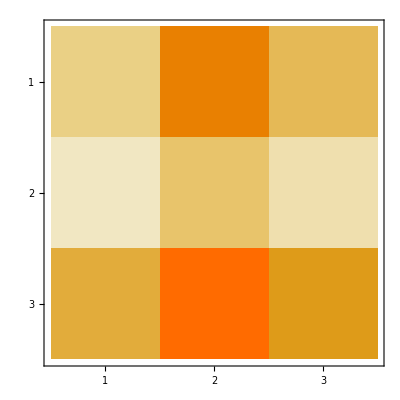

```mathematica
For[i=1,i≤iter,i++,
For[j=1,j≤Length[Bmatrix2[1][[i]]],j++,
For[k=1,k≤Length[Bmatrix2[1][[i,j]]],k++,
If[i==1,
stdprep[j,k]={}
];
stdprep[j,k]=Join[stdprep[j,k],{Bmatrix2[1][[i,j,k]]}]
]
];
]
For[l=1,l≤iter,l++,
For[m=1,m≤Length[Bmatrix2[1][[l]]],m++,
For[n=1,n≤Length[Bmatrix2[1][[l,m]]],n++,
stdfunc[m,n]=StandardDeviation[stdprep[m,n]];
meanfunc[m,n]=Mean[stdprep[m,n]]
]
]
]
stdarray=Array[stdfunc,{3,3}];
meanarray=Array[meanfunc,{3,3}];
MatrixPlot[stdarray]
```

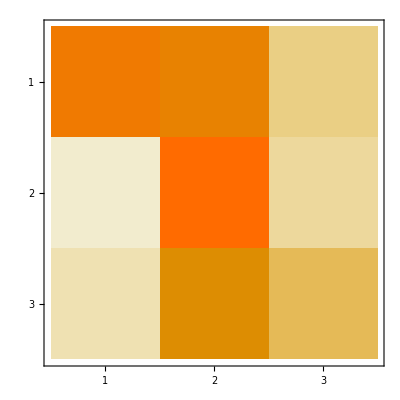

```mathematica
MatrixPlot[Abs[Bmatrix[1]-meanarray]]
```

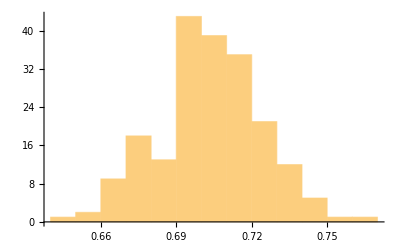

0.703648

0.707983

```mathematica
Histogram[stdprep[1,1]]
meanarray[[1,1]]
Bmatrix[1][[1,1]]
```

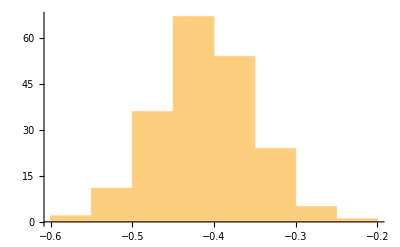

-0.412056

-0.407981

```mathematica
Histogram[stdprep[1,2]]
meanarray[[1,2]]
Bmatrix[1][[1,2]]
```

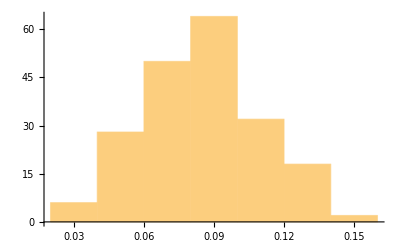

0.0854756

0.0861775

```mathematica
Histogram[stdprep[1,3]]
meanarray[[1,3]]
Bmatrix[1][[1,3]]
```

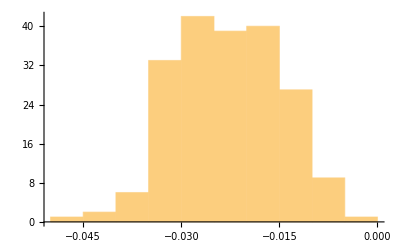

-0.0228351

-0.0227186

```mathematica
Histogram[stdprep[2,1]]
meanarray[[2,1]]
Bmatrix[1][[2,1]]
```

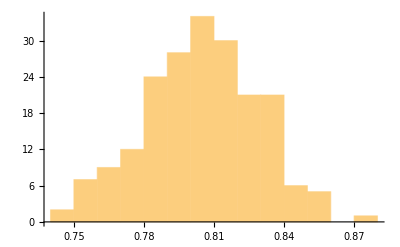

0.804758

0.80994

```mathematica
Histogram[stdprep[2,2]]
meanarray[[2,2]]
Bmatrix[1][[2,2]]
```

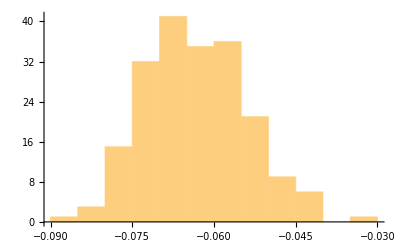

-0.0632828

-0.0627321

```mathematica
Histogram[stdprep[2,3]]
meanarray[[2,3]]
Bmatrix[1][[2,3]]
```

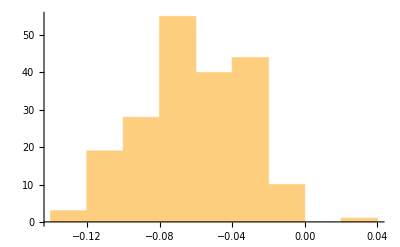

-0.0615642

-0.061149

```mathematica
Histogram[stdprep[3,1]]
meanarray[[3,1]]
Bmatrix[1][[3,1]]
```

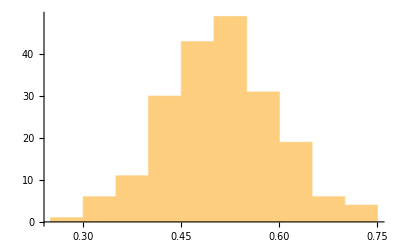

0.509633

0.506034

```mathematica
Histogram[stdprep[3,2]]
meanarray[[3,2]]
Bmatrix[1][[3,2]]
```

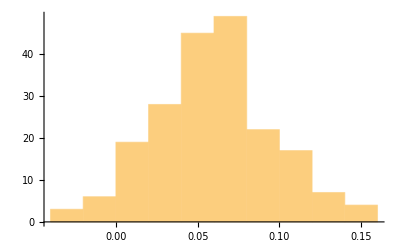

0.0592742

0.060775

```mathematica
Histogram[stdprep[3,3]]
meanarray[[3,3]]
Bmatrix[1][[3,3]]
```

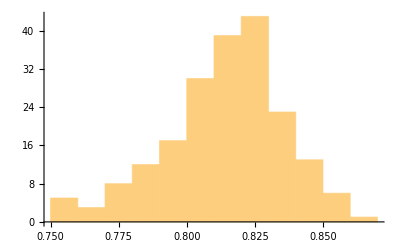

0.814326

0.820138

```mathematica
maxeiglist={};
For[i=1,i≤Length[Bmatrix2[1]],i++,
maxeiglist=Join[maxeiglist,{Max[Re[Eigenvalues[Bmatrix2[1][[i]]]]]}]
]
Histogram[maxeiglist]
Mean[maxeiglist]
Max[Re[Eigenvalues[Bmatrix[1]]]]
```